### 1. Init (RUN)

```mathematica
V[s_]:=1/2k s^2;
q={p[t],l[t]};
dq={p'[t],l'[t]};
(*
eomL=D[D[L,{dq}],t]-D[L,{q}]*)
```

```mathematica
getEOM[a_,ss_]:=Module[{A=D[a,{q}],M,G,Υ,eoms,ke},
ke=1/2m p'[t]^2+V[ss[p[t]]]+1/2ml l'[t]^2;
M=D[ke,{dq,2}];
Ma=ArrayFlatten[{{M,Aᵀ},{A,0}}];
G={D[V[ss[p[t]]],p[t]],0};
Υ={0,ul};
(*Print["HI",A];*)
eoms=Inverse[Ma].Join[Υ-G,-D[A,t].dq]//Simplify;
(*Print[Inverse[Ma]//MatrixForm];*)
{eoms,Join[Inverse[M].(Υ-G),{0}],Ma}
];
(*1DOF vertical-only example*)
getEOM[{p[t]-l[t]},(#-p0)&]
```

{{(k p0+ul-k p[t])/(m+ml),(k p0+ul-k p[t])/(m+ml),(k ml p0-m ul-k ml p[t])/(m+ml)},{-(k (-p0+p[t]))/m,ul/ml,0},{{m,0,1},{0,ml,-1},{1,-1,0}}}

```mathematica
(*Run a sim*)
runSim[lvel_,eoms2_,sfunc_,params_,pi0_,l0_,ctype_:1]:=Module[{trel=0,tTO=100,T=5,sol,velTO=0,ic},
ic={p[0]==pi0,l[0]==l0,p'[0]==0,l'[0]==0,c[0]==1};
Print["lvel=",lvel];
sol=First@NDSolve[
Join[eoms2/.ul->kvel(lvel-If[ctype==1,l'[t],p'[t]])/.params,ic,{
WhenEvent[λ[t]>0,{c[t]->0,trel=t,Print["Release at t=",t]}],
WhenEvent[(sfunc[p[t]]/.params)==0,{tTO=t,velTO=p'[t],Print["Takeoff at t=",t,", vel=",velTO],"StopIntegration"}]
}],
{p,l,λ,c},{t,0,T},DiscreteVariables->{c}];
T=Min[T,tTO];
Return[{{sol,T,trel,tTO},velTO}]
];

(*Plots with Ep*)
phasePlot[{sol_,T_,trel_,tTO_},params_,Ep_,p2E_:True]:=Show[{
ParametricPlot[Evaluate[{p[t],If[p2E,Ep/.params,p'[t]]}/.sol],{t,0,T},AxesLabel->{p,If[p2E,"E",p']},AspectRatio->1,GridLines->Automatic,PlotStyle->Blue]/.Line[x_]:>{Arrowheads[{0.,0.07,0.07,0.07,0.}],Arrow[x]},
Graphics[{PointSize[Large],Red,Opacity[1],Point[Evaluate[{
{p[trel],If[p2E,Ep/.sol/.t->trel/.params,p'[trel]]},{p[tTO],If[p2E,Ep/.sol/.t->tTO/.params,p'[tTO]]}
}/.sol]]}]
}]

ePlot[{sol_,T_,trel_,tTO_},params_,Ep_]:=Show[{
Plot[Ep/.params/.sol,{t,0,T},PlotLabel->"E",PlotStyle->Blue],
Graphics[{PointSize[Large],Red,Opacity[1],Point[Evaluate[{
{trel,Ep/.sol/.t->trel/.params},{tTO,Ep/.sol/.t->tTO/.params}
}/.sol]]}]
}]

(*Results of a one-off sim*)
displaySim[{sol_,T_,trel_,tTO_},sfunc_,params_,Ep_,drawFunc_]:=Module[{},
{
Animate[drawFunc[tt,sol],{tt,0,T},AnimationRate->1,AnimationRepetitions->1],
Plot[Evaluate[{
Legended[1/2m p'[t]^2,"p KE"],
Legended[V[sfunc[p[t]]],"p PE"],
(*Legended[1/2ml l'[t]^2,"l KE"],*)
Legended[Ep,"Total"]
}/.sol/.params],{t,0,T},PlotLabel->"Energy",GridLines->{{trel},None}],
Plot[Evaluate[{
Legended[aa,"a"],
Legended[λ[t],"λ"],
Legended[c[t],"c"]
}/.sol/.params],{t,0,T},PlotLabel->"Constraint",GridLines->{{trel},None}],
Plot[Evaluate[{
Legended[l'[t],"l"]
}/.sol/.params],{t,0,T},PlotLabel->"ldot",GridLines->{{trel},None}],
phasePlot[{sol,T,trel,tTO},params,Ep]
}
];

simAnim[{sol_,T_,trel_,tTO_},drawFunc_,fname_,tint_:1/30]:=Export[NotebookDirectory[]<>fname,Table[drawFunc[tt,sol],{tt,0,T,tint}]]
```

### 2. Round latch (RUN)

```mathematica
params={m->1,ml->1,k->1,R->1,p0->1,dx->1,dy->0.5,kvel->1000};
scl:=#-p0&;
(*Curved latch*)
aa={l[t]^2+(R-p[t])^2-R^2};
drawThings[tt_,sol_]:=Module[{},
Graphics[{
EdgeForm[Thick],
Orange,Disk[{l[t],R},R,{π,3π/2}],
Blue,Rectangle[{-dx,p[t]-dy},{0,p[t]}],
Thick,Black,
Line[{{-dx/2,-1},{-dx/2,p[t]-dy}}],
Text[tt,{-0.5,-1.5}]
},PlotRange->3R{{-1,1},{-1,1}},GridLines->Automatic,ImageSize->Small]/.sol/.t->tt/.params
];
(*Solve*)
{eunlatching,eact,Ma}=getEOM[aa,scl];
Off[NDSolve::pdord];
eoms1=Thread[{p''[t],l''[t],λ[t]}==c[t]eunlatching+(1-c[t])eact];
eoms2=eoms1/.params;

(*Total energy of the projectile*)
Clear[Ep];
Ep=1/2m p'[t]^2+V[scl[p[t]]];

(*Analysis*)
lmode1=Last@Solve[aa[[1]]==0,l[t]];
λforlvel[lvel_]:=eoms1[[-1]][[-1]]/.lmode1/.{ul->0,c[t]->1,l'[t]->lvel,p'[t]->vp,p[t]->pp}
lvelforλ0=lv/.Last@Solve[λforlvel[lv]==0,lv]/.params;
lvelforλ0E=lvelforλ0/.(First@Solve[(Ep/.{p'[t]->vp,p[t]->pp})==Eep,vp]/.params);
(*Above this it is an instantaneous latch*)
lvelThresh=lvelforλ0/.{pp->0,vp->0}
```

1

### 3. Round latch new analysis

```mathematica
(*NEW ANALYSIS: Last row of MAinv*)
e3TMAi={(2 ml R-2 ml p[t])/(-4 ml R^2-4 m l[t]^2+8 ml R p[t]-4 ml p[t]^2),-(2 m l[t])/(-4 ml R^2-4 m l[t]^2+8 ml R p[t]-4 ml p[t]^2),(m ml)/(-4 ml R^2-4 m l[t]^2+8 ml R p[t]-4 ml p[t]^2)};
(e3TMAi.{-g,0,-dAdq}/.m->ϵ ml/.ml->m/ϵ)(*/.ϵ->0*)//Simplify
(*D[D[aa,{q}],t].dq//Simplify
D[aa,{q}].dq//Simplifyz
aa//Simplify
lv/.Last@Solve[λforlvel[lv]==0,lv]*)
(*Plot[vl^2/(R(1-v*)
```

(dAdq m+2 g R-2 g p[t])/(4 (ϵ l[t]^2+(R-p[t])^2))

Sym inverse {(-R+p[t])/(2 (ϵ l[t]^2+(R-p[t])^2)),(ϵ l[t])/(2 (ϵ l[t]^2+(R-p[t])^2)),-m/(4 (ϵ l[t]^2+(R-p[t])^2))} vs. new {-(2 (R-p[t]))/m,(2 l[t])/ml}

k (-p0+p[t])

Check with constraint Hessian 0

Unlatch evt = -2 vl^2-(2 t^2 vl^4)/(R^2-t^2 vl^2)+(2 k √(R^2-t^2 vl^2) (p0-R+√(R^2-t^2 vl^2)))/m

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

2.88443

7.74966

0.562475

1.68713

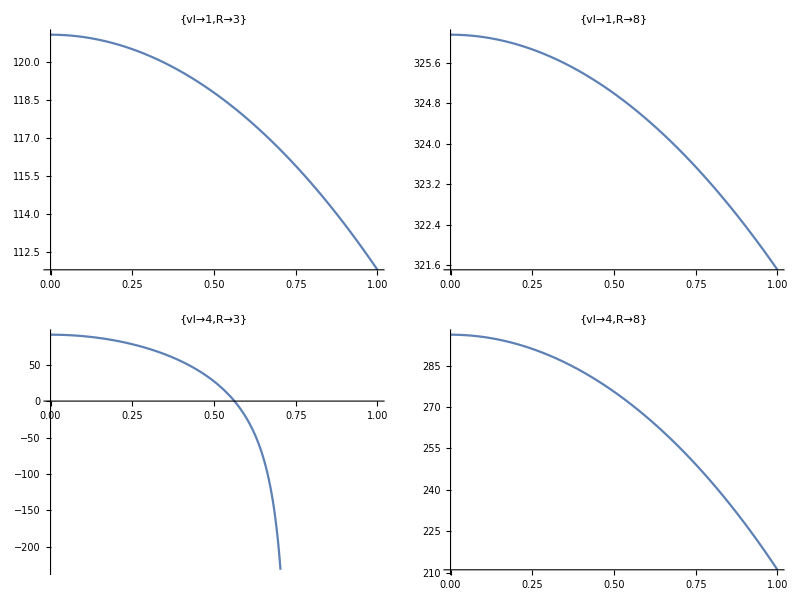
(-Graphics-)

```mathematica
(*NEW NEW*)
Ap=Ma[[3,1]];
Al=Ma[[3,2]];
Aa=Ma[[3,1;;2]];
Print["Sym inverse ",(e3TMAi(*.{-g,0,-dAdq}*)/.m->ϵ ml/.ml->m/ϵ)(*/.ϵ->0*)//Simplify," vs. new ",
(*Analytically invert, leave out scalar α*)
Ma[[3,1;;2]].DiagonalMatrix[{1/m,1/ml}]];

params2={m->1000,Fs->20510,p0->10,k->2051,vlMAX->10,E0->2000000};

HOOKE=True;
G=If[HOOKE,D[V[scl[p[t]]],{p[t]}],-Fs]
(*General version*)
Print["Check with constraint Hessian ",D[Aa,t].dq-dq.D[Aa,{q}].dq//Simplify];
unlatchingSubs=Join[First@Solve[Aa.dq==0,p'[t]],First@Solve[aa==0,p[t]]];
Print["Unlatch evt = ",unlatchEvt=((Ap/m G-D[Aa,t].dq)//.unlatchingSubs/.{l'[t]->vl,l[t]->vl t})//Simplify];
(*The Min is more correct but makes it non-smooth, and the result for HOOKE seems the same with or without*)
unlatchtsol=(*Min[*)Re[t/.Solve[unlatchEvt==0,t][[4]]](*,R/vl]*);

(*Test unlatch event*)
testPlotEvt[subs_]:=Module[{tul=unlatchtsol/.params2/.subs},
Print[tul//N];
Plot[unlatchEvt/.subs/.params2,{t,0,1},GridLines->{{tul},None},PlotLabel->subs]
];
Table[testPlotEvt[{vl->vli,R->Ri}],{vli,{1,4}},{Ri,{3,8}}]//MatrixForm
(*This makes sense; bigger latch takes longer for the same *)
```

```mathematica
(*analytical assuming constant Fs*)
unlatchtsolA1 =1/vl Sqrt[R^2-(m vl^2R^2/Fs)^(2/3)];
unlatchtsolA =Re[unlatchtsolA1];
```

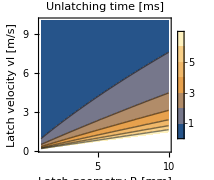

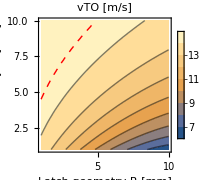

```mathematica
(*Fully analytical expression for the unlatching state*)
unlatchState={p[t],p'[t]}//.unlatchingSubs/.{l'[t]->vl,l[t]->vl tul};

(*Try to replicate the heatmap from the latch presentation*)
unlatchE=Sqrt[2*(1/2 m unlatchState[[2]]^2+V[scl[unlatchState[[1]]]])/m];

(*ContourPlot[R/vl,{

R,1,10},{vl,1,10},FrameLabel->{"Latch geometry R [mm]","Latch velocity vl [m/s]"},PlotLegends->Automatic,PlotLabel->"Unlatching time [ms]"],*)
ContourPlot[unlatchtsolA/.params2,{R,1,10},{vl,0.1,10},FrameLabel->{"Latch geometry R [mm]","Latch velocity vl [m/s]"},PlotLegends->Automatic,PlotLabel->"Unlatching time [ms]",ImageSize->Small]
Show[{
ContourPlot[unlatchE/.tul->unlatchtsolA/.params2,{R,1,10},{vl,1,10},FrameLabel->{"Latch geometry R [mm]","Latch velocity vl [m/s]"},PlotLegends->Automatic,PlotLabel->"vTO [m/s]",ImageSize->Small],
ContourPlot[unlatchtsolA1/.params2,{R,1,10},{vl,1,10},ContourShading->None,Contours->{0.01},ContourStyle->Directive[Dashed,Red]]
}]
(*Export[NotebookDirectory[]<>"unlatch2.pdf",%]*)
```

#### Hooke-like standard spring

-Graphics-

Re[(√(R^2-((-(2^(-1+n) 5^(-2+n) m (-p0)^(1-n) R^2 vlMAX^2)/n)^(2/3))/2051^(2/3)))/vlMAX]

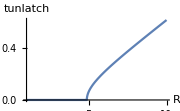

```mathematica
(*Design space simplified*)
(*Normalized so that the total energy stored at p=0 is the same*)
V2[s_,n_]:=1/2knorm s^n/.({knorm->k p0^(2-n)}/.params2);
(*Would like an expression for the max potential energy that can be converted to KE, as a func of ζ as well*)
(*χ[t]/.First@DSolve[χ''[t]+2ζ ωn χ'[t]+ωn^2 χ[t]==0,χ,t]//Simplify*)
(*http://web.mst.edu/~stutts/SupplementalNotes/EqivalentViscousDamping.pdf*)
(*kd ω^2X^2Integrate[Cos[ω t-ϕo]^2,{t,0,π/(2ω)}]/.{ϕo->π/2,kd->2 ζ ω,X->p0}*)
Clear[Wd];
Wd[s_,ζ_]:=2ζ ω^3(p0-s)^2Integrate[Cos[x]^2,{x,0,π/2}]/.{ω->Sqrt[k/m]}
V2rel[s_,n_,ζ1_]:=V2[s,n]-Wd[s,ζ1]

(*Cannot get instantaneous release (assume finite latch power), especially at higher R*)
minUnlatchTime=unlatchtsolA/.{Fs->-(D[V2[scl[p],n],p]/.p->0),vl->vlMAX}
(*Limit[unlatchtsolA,vl->0]*)
Plot[minUnlatchTime/.n->2/.params2,{R,1,10},ImageSize->Small,AxesLabel->{R,tunlatch}]
Emin=V2rel[-scl[R],n,(*ζ*)10];
unlatchE2=(1/2 m unlatchState[[2]]^2+V2rel[-scl[unlatchState[[1]]],n,(*ζ*)0])/.params2;
Emax=unlatchE2/.{tul->minUnlatchTime,vl->vlMAX}/.params2;
```

#### Metamaterial spring

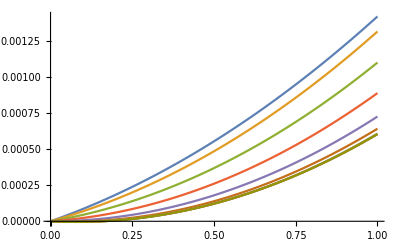
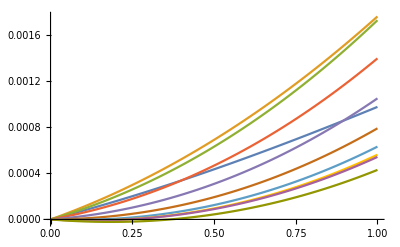

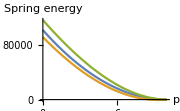

```mathematica
(*For metamaterial spring*)
c1=Interpolation[{{0.1,-0.008},{0.2,-0.0063},{0.3,-0.0038},{0.4,-0.0016},{0.5,0},{0.6,0.0008},{0.7,0.0011},{0.8,0.0011},{0.9,0.0011},{1.0,0.0011}}];
c2=Interpolation[{{0.1,0.0611},{0.2,0.0673},{0.3,0.0706},{0.4,0.0714},{0.5,0.0712},{0.6,0.0708},{0.7,0.0704},{0.8,0.0702},{0.9,0.0701},{1.0,0.0701}}];
c3=Interpolation[{{0.1,-0.007},{0.2,-0.0109},{0.3,-0.0129},{0.4,-0.0134},{0.5,-0.0132},{0.6,-0.0130},{0.7,-0.0127},{0.8,-0.0126},{0.9,-0.0125},{1.0,-0.0125}}];
(*Note at 0.1 have different signs so the fitting is weird*)
d1=Interpolation[{{0.1,-0.00733},{0.2,-0.01010},{0.3,-0.00822},{0.4,-0.00501},{0.5,-0.00213},{0.6,-0.00011},{0.7,0.00106},{0.8,0.00154},{0.9,0.00158},{1.0,0.00231}}];
d2=Interpolation[{{0.1,0.02932},{0.2,0.07198},{0.3,0.08441},{0.4,0.08285},{0.5,0.07732},{0.6,0.07203},{0.7,0.06825},{0.8,0.06623},{0.9,0.06491},{1.0,0.06140}}];
d3=Interpolation[{{0.1,0.04836},{0.2,-0.0271},{0.3,-0.05667},{0.4,-0.06246},{0.5,-0.05970},{0.6,-0.05535},{0.7,-0.05183},{0.8,-0.05007},{0.9,-0.04834},{1.0,-0.04422}}];
d4=Interpolation[{{0.1,-0.03742},{0.2,0.00036},{0.3,0.01663},{0.4,0.02106},{0.5,0.02088},{0.6,0.01953},{0.7,0.01829},{0.8,0.01774},{0.9,0.01693},{1.0,0.01518}}];
(*For the dynamic Phiv to use in the release phase. (1) from Xudong*)
mmΦs[s_,ar_]:=E0(c1[ar]ϵ+c2[ar]ϵ^2+c3[ar]ϵ^3)/.{ϵ->-s/(p0)}
(*This is the dynamic recoil (max energy that can be extracted. Use this to predict the release energy. (2) from Xudong*)
mmΦv[s_,ar_]:=E0(d1[ar]ϵ+d2[ar]ϵ^2+d3[ar]ϵ^3+d4[ar]ϵ^4)/.{ϵ->-s/(p0)}
(*Also including the α parameter. Eqns (3) (4) from Xudong*)
Vmm[s_,ar_,α_]:=(1+α)mmΦs[s,ar]
Vmmrel[s_,ar_,α_]:=mmΦv[s,ar]+α mmΦs[s,ar]
(*Confirm by comparing to Xudong plots*)
{
Plot[Evaluate@Table[mmΦs[ϵ,ar]/E0/.params2,{ar,0.1,1,0.1}],{ϵ,0,1}],
Plot[Evaluate@Table[mmΦv[ϵ,ar]/E0/.params2,{ar,0.1,1,0.1}],{ϵ,0,1}]
}

(*Normalization*)
Plot[{Legended[V2[scl[p],2]/.params2,"Hooke"],Legended[Vmm[scl[p],0.1,0]/.params2,"MM 0.1"],Legended[Vmm[scl[p],1.0,0]/.params2,"MM 1.0"]},{p,0,10},AxesLabel->{p,"Spring energy"},ImageSize->Small]
(*Export[NotebookDirectory[]<>"mmnorm.pdf",%]*)

(*Functions for release energy*)
Efinalmm[R1_,ar_,vl1_,α_]:=((1/2 m unlatchState[[2]]^2+Vmmrel[scl[unlatchState[[1]]],ar,α])/.tul->unlatchtsolA1/.{Fs->-(D[Vmm[scl[p],ar,α],p]/.p->0)})/.{vl->vl1,R->R1}/.params2;
(*Min w.r.t. vL*)
EminvLmm[R1_,ar_,α_]:=Vmmrel[scl[R1],ar,α]/.params2;
(*Cannot get instantaneous release (assume finite latch power), especially at higher R. Use the static one for unlatching*)
minUnlatchTime=unlatchtsolA/.{Fs->-(D[Vmm[scl[p],ar,α],p]/.p->0),vl->vlMAX};
```

### Latch inertia >> proj inertia sim

```mathematica
(*Use analytical inverse of the Ma matrix*)
Mainv[A_]:=Module[{Minv=DiagonalMatrix@{1/m,(*1/ml*)0},α,Mai11,Mai12,Mai21,Mai22},
(*In the notation of the wiki article, α=(M/A)^{-1}*)
α=-Inverse[A.Minv.Aᵀ];
Mai21=-α.A.Minv;
Mai22=α;
Mai11=Minv+Minv.Aᵀ.α.A.Minv;
Mai12=-Minv.Aᵀ.α;
Return[{Minv,ArrayFlatten[{{Mai11,Mai12},{Mai21,Mai22}}]}]
];
newRHS[{A_,s_,V_}]:=Module[{Fs=-D[V[s[q⟦1⟧]],{q}],Minv,Mai},
{Minv,Mai}=Mainv[A];
{Mai.Join[Fs,-D[A,t].dq],Join[Minv.Fs,{0}]}//Simplify
];
Clear[newSim];
newSim[{A_,s_,V_},pi0_,l0_,vl_,params_,T_]:=Module[{
rhs=newRHS[{A,s,V}],eom,ic,sol,trel,tTO
},
eom=Thread[Join[D[dq,t],{λ[t]}]==c[t]*rhs[[1]]+(1-c[t])*rhs[[2]]];
ic={l'[0]==vl,p[0]==pi0,l[0]==l0,p'[0]==0,c[0]==1}/.params;
(*Print[Join[eom,ic]];*)
sol=First@NDSolve[Join[eom,ic,{
WhenEvent[λ[t]>0,{c[t]->0,trel=t(*,Print["Release at t=",t,", state=",{p[t],p'[t]}]*)}],
WhenEvent[(s[p[t]]/.params)==0,{tTO=t,velTO=p'[t](*,Print["Takeoff at t=",t,", vel=",velTO]*),"StopIntegration"}]}]/.params,{p,l,λ,c},{t,0,T},DiscreteVariables->{c},AccuracyGoal->4];
{sol,trel,tTO}
];
phasePlot2[{sol_,trel_,tTO_},params_,dpmax_,color_:{}]:=Module[{},
Show[{
ParametricPlot[{p[t],p'[t]}/.sol,{t,0,tTO},AspectRatio->1,GridLines->Automatic,PlotStyle->If[Length[color]==0,Blue,color],ImageSize->150,Axes->False,Frame->True,PlotRange->{{0,p0/.params},{0,dpmax}},FrameLabel->{"p","dp"}]/.Line[x_]:>{Arrowheads[{0.,0.07,0.07,0.07,0.}],Arrow[x]},
Graphics[{PointSize[Large],Red,Opacity[1],Point[Evaluate[{
{p[trel],p'[trel]}(*,{p[tTO],p'[tTO]}*)
}/.sol]]}]
}]
];
streams2[{sol_,trel_,tTO_},{A_,s_,V_},params_,dpmax_]:=
StreamPlot[{dpp,newRHS[{A,s,V}][[2]][[1]]/.params/.p[t]->pp},{pp,0,p0/.params},{dpp,0,dpmax},StreamStyle->Directive[Red,Opacity[0.3]]]

combinedPlot2[ress_,{A_,s_,V_},params_,dpmax_,des_,colors_:{}]:=Module[{unlatchState2,fnpdp},
(*unlatchState defined above*)
unlatchState2=unlatchState/.tul->unlatchtsolA1/.des/.params;
(*unlatchState2/.vl->5//N*)
(*This function is 0 at the unlatch state (of (pp,dp))*)
fnpdp=(unlatchState2[[2]]/.Last@Solve[unlatchState2[[1]]==pp,vl])-dp;
Show[Join[
Table[phasePlot2[ress[[i]],params,dpmax,If[Length[colors]>0,colors[[i]],{}]],{i,Length@ress}],{
streams2[ress[[1]],{A,s,V},params,dpmax],
RegionPlot[fnpdp>0,{pp,0,10},{dp,0,15}]
}]]
];
basicPlots[{sol_,trel_,tTO_}]:={
Plot[p[t]/.sol,{t,0,tTO}],
(*Plot[l'[t]/.sol,{t,0,tTO}],*)
Plot[c[t]/.sol,{t,0,tTO}],
Plot[λ[t]/.sol,{t,0,tTO},PlotRange->All],
Plot[aa/.sol,{t,0,tTO},PlotRange->All]
}
```

#### Different design points

```mathematica
roundLatchHookes[Rr_,nn_]:=Module[{des=R->Rr,aa,scl,Aa,Vhl,Vhl2},
aa={l[t]^2+(R-p[t])^2-R^2}/.des;
scl:=#-p0&;
Vhl[s_,n_]:=1/2k s^n;
Vhl2[s_]:=Vhl[s,nn];
Aa=D[aa,{q}];
Return[{{Aa,scl,Vhl2},des}]
];
roundLatchMeta[Rr_,arr_]:=Module[{des=R->Rr,aa,scl,Aa,Vmm,Vhl2a},
aa={l[t]^2+(R-p[t])^2-R^2}/.des;
scl:=#-p0&;
Vmm[s_,ar_]:=E0(c1[ar]ϵ+c2[ar]ϵ^2+c3[ar]ϵ^3)/.{ϵ->-s/(p0)};
Vhl2a[s_]:=Vmm[s,arr];
Aa=D[aa,{q}];
Return[{{Aa,scl,Vhl2a},des}]
];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

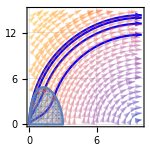
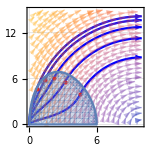

C:\Users\Wyss User\Downloads\control_paper_sims\nsphase.pdf

```mathematica
{AsV,des}=roundLatchHookes[3,2];
ress=Table[newSim[AsV,0,0,vl,params2,6],{vl,1,8,2}];
P32=combinedPlot2[ress,AsV,params2,15,des];
{AsV,des}=roundLatchHookes[6,2];
ress=Table[newSim[AsV,0,0,vl,params2,20],{vl,1,10,2}];
P62=combinedPlot2[ress,AsV,params2,15,des];
{P32,P62}
Export[NotebookDirectory[]<>"Figure5CD.pdf",%]
(*{AsV,des}=roundLatchMeta[4.5,0.1];
MR45a01=combinedPlot2[Table[newSim[AsV,0,0,vl,params2,20],{vl,1,10,2}],
AsV,params2,15,des];
{AsV,des}=roundLatchMeta[4.5,1];
MR45a10=combinedPlot2[Table[newSim[AsV,0,0,vl,params2,20],{vl,1,10,2}],
AsV,params2,15,des];
{AsV,des}=roundLatchMeta[8,0.1];
MR80a01=combinedPlot2[Table[newSim[AsV,0,0,vl,params2,20],{vl,1,10,2}],
AsV,params2,15,des];
{AsV,des}=roundLatchMeta[8,1];
MR80a10=combinedPlot2[Table[newSim[AsV,0,0,vl,params2,20],{vl,1,10,2}],
AsV,params2,15,des];
{MR45a01,MR45a10,MR80a01,MR80a10}
Export[NotebookDirectory[]<>"mmphase.pdf",{MR45a01,MR80a10}]*)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

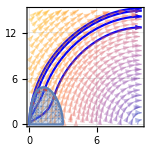
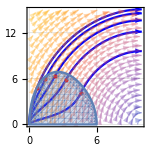

C:\Users\Wyss User\Downloads\control_paper_sims\mmphase.pdf

```mathematica
{AsV,des}=roundLatchMeta[3,0.5];
MR30a05=combinedPlot2[Table[newSim[AsV,0,0,vl,params2,20],{vl,1,7,2}],
AsV,params2,15,des];
{AsV,des}=roundLatchMeta[6,0.5];
MR60a05=combinedPlot2[Table[newSim[AsV,0,0,vl,params2,20],{vl,1,9,2}],
AsV,params2,15,des];
{MR30a05,MR60a05}
Export[NotebookDirectory[]<>"Figure5EF.pdf",{MR30a05,MR60a05}]
```

#### Stabilizability

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

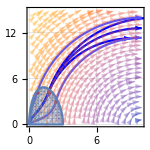
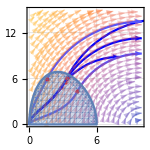

C:\Users\Wyss User\Downloads\control_paper_sims\nss.pdf

```mathematica
(*Next need a plot w.r.t p0 (for the stabilizability).Have p0 as an axis?No,better to have different traces with different p0 somehow (just as in this plot have different traces with different vl--referring to the phase-space plot). Use the simulation to vary p0, *)
newSimP0[{A_,s_,V_},pi0_,l0_,vl_,params_,T_,p0new_]:=Module[{params3=ReplacePart[params,3->(p0->p0new)]},
(*The position is hardcoded FIXME*)
newSim[{A,s,V},pi0,l0,vl,params3,T]
];
(*params2*)
{AsV,des}=roundLatchHookes[3,2];
vlp0pairs={{2,9},{2,10},{2,11},{0.65,10},{5,10}};
stabR3=combinedPlot2[Table[newSimP0[AsV,0,0,vlp0[[1]],params2,6,vlp0[[2]]],{vlp0,vlp0pairs}],
AsV,params2,15,des,{Blue,Blue,Blue,Lighter[Blue],Lighter[Blue]}];
{AsV,des}=roundLatchHookes[6,2];
vlp0pairs={{3,8},{3,10},{3,12},{1.3,10},{6.5,10}};
stabR6=combinedPlot2[Table[newSimP0[AsV,0,0,vlp0[[1]],params2,6,vlp0[[2]]],{vlp0,vlp0pairs}],
AsV,params2,15,des,{Blue,Blue,Blue,Lighter[Blue],Lighter[Blue]}];
{stabR3,stabR6}
Export[NotebookDirectory[]<>"Figure6CD.pdf",%]
```

```mathematica
params2
```

{m→1000,Fs→20510,p0→10,k→2051,vlMAX→10,E0→2000000}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

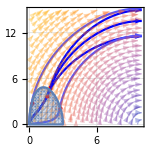
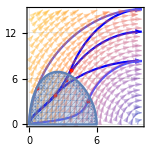

C:\Users\Wyss User\Downloads\control_paper_sims\Figure5EF.pdf

```mathematica
Clear[newSimE0];
newSimE0[{A_,s_,V_},vl_,params_,T_,E0new_]:=Module[{params3=ReplacePart[params,6->(E0->E0new)]},
(*The position is hardcoded FIXME*)
newSim[{A,s,V},0,0,vl,params3,T]
];
{AsV,des}=roundLatchMeta[3,0.5];
vlE0pairs={{2,2*10^6},{2,2.5*10^6},{2,1.4*10^6},{0.2,2*10^6},{7,2*10^6}};
stabR3=combinedPlot2[Table[newSimE0[AsV,vlp0[[1]],params2,20,vlp0[[2]]],{vlp0,vlE0pairs}],
AsV,params2,15,des,{Blue,Blue,Blue,Lighter[Blue],Lighter[Blue]}];
{AsV,des}=roundLatchMeta[6,0.5];
vlE0pairs={{3,2*10^6},{3,3.5*10^6},{3,0.75*10^6},{0.4,2*10^6},{9,2*10^6}};
stabR6=combinedPlot2[Table[newSimE0[AsV,vlp0[[1]],params2,30,vlp0[[2]]],{vlp0,vlE0pairs}],
AsV,params2,15,des,{Blue,Blue,Blue,Lighter[Blue],Lighter[Blue]}];
{stabR3,stabR6}
Export[NotebookDirectory[]<>"Figure6EF.pdf",%]
```